```mathematica
<<peeters` ;
peeters`setGitDir[ "blogit" ]
```

C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit

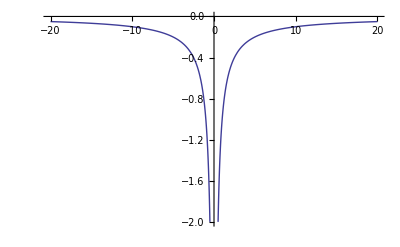

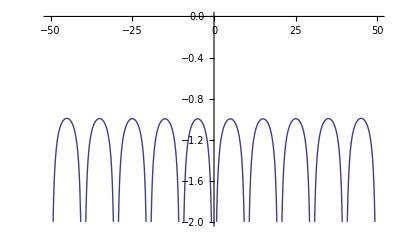

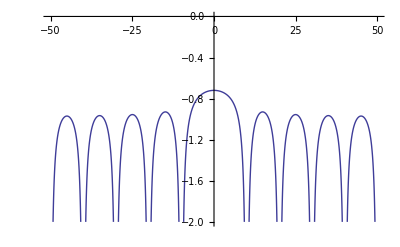

```mathematica
Clear[ f, g, h, l, a ] ;
f[ r_ ] = -Sqrt[ 1/r^2 ] ;
a = 10 ;
l = 20 a ;
g[ r_, m_, n_] := Sum[ f[r + k ], {k, m, n, a}] ;

h[ r_ ] = g[ r, -l, l ] ;
v[ r_ ] = g[ r, -l, -a] + g[ r, a, l ] ;

Clear[p1, p2, p3]

p1 = Plot[ f[r], {r, -2 a, 2 a}, PlotRange -> {Automatic, {-2, 0}} ]
p2 = Plot[ h[r], {r, -l/4, l/4}, PlotRange -> {Automatic, {-2, 0}}]
p3 = Plot[ v[r], {r, -l/4, l/4}, PlotRange -> {Automatic, {-2, 0}}]
```

```mathematica
peeters`exportForLatex["tightBindingInverseRadialPotentialFig1", p1]
peeters`exportForLatex["tightBindingInverseRadialPotentialPeriodicFig2", p2]
peeters`exportForLatex["tightBindingInverseRadialPotentialPeriodicOneMissingFig3", p3]
```

{C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit/tightBindingInverseRadialPotentialFig1.eps,C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit/tightBindingInverseRadialPotentialFig1pn.png}

{C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit/tightBindingInverseRadialPotentialPeriodicFig2.eps,C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit/tightBindingInverseRadialPotentialPeriodicFig2pn.png}

{C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit/tightBindingInverseRadialPotentialPeriodicOneMissingFig3.eps,C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit/tightBindingInverseRadialPotentialPeriodicOneMissingFig3pn.png}